```mathematica
If[!NumberQ[makePallette],NotebookEvaluate[NotebookDirectory[]~~"visualVocabDefs.nb"],NotebookEvaluate[NotebookDirectory[]~~"vvClear.nb"]];
```

## Design of Linear Filters

A basic strategy in the design of linear filters is to specify the desired behavior of the filter in the frequency domain. Once specified, the frequency response can be inverted back into the time (or space) domain where it can be sampled and implemented straightforwardly using functions like ListConvolve[ ]. Two variations of this strategy are discussed here. The first is an analytical approach where the filter is specified as a continuous function of frequency which is inverted symbolically. Then the inverted function is sampled to give the kernel (the coefficients of the digital filter). The second approach is a numerical approach which samples the desired function (or directly specifies the desired in numerical form). The specification is then inverted numerically and truncated to give the kernel. Each of the methods is applied to the design of a bandpass filter, though it should be straightforward to specify and design almost any desired filter using the same basic ideas. The third section condenses the (somewhat lengthy exposition) into a simple function that is easy to call. Then the whole exercise is repeated in two dimensions, where the same basic ideas apply.

```mathematica
TableForm[{{Hyperlink["FilterOrder",{"vvFilterDesign.nb","labelFilterOrder"},BaseStyle->mathColor],labelFilterOrder},{Hyperlink["FilterSpec",{"vvFilterDesign.nb","labelFilterSpec3"},BaseStyle->mathColor],labelFilterSpec3}}]
```

| Increase filter order to get closer to specification
 | A bandpass filter that passes frequencies between f and 1.01f

### Analytic Design of a Band Pass Filter

Specifying a filter in the frequency domain is as easy as creating a function that has the desired shape. For each possible frequency, the frequency response shows how much to attenuate or amplify that frequency. The procedure works most smoothly when the chosen frequency domain response is invertible symbolically. For example, suppose that it is desired to create a filter that removes all the low and all the high frequencies, leaving only the midrange frequencies intact. This can be specified and plotted by creating a function of frequency called bandPassSpec[ ]

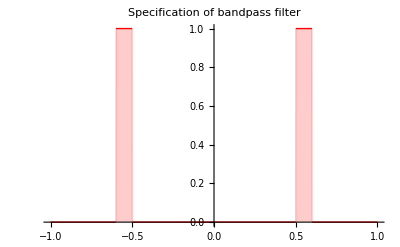

```mathematica
bandPassSpec[ω_]:=UnitStep[ω+0.6]-UnitStep[ω+0.5] +UnitStep[ω-0.5]-UnitStep[ω-0.6];
Plot[bandPassSpec[ω],{ω,-1,1},PlotStyle->{Hue[0],Thick},Filling->Axis,PlotLabel->"Specification of bandpass filter"]
```

The inverse transform of bandPassSpec is the continuous time bandpass kernel

```mathematica
bandPassKer[n_]:=FullSimplify[InverseFourierTransform[bandPassSpec[ω/Pi],ω,n,FourierParameters->{1,-1}]];
bandPassKer[n]
```

(ⅈ ⅇ^((0.-3.45575 ⅈ) n) (ⅇ^((0.+1.5708 ⅈ) n)-ⅇ^((0.+1.88496 ⅈ) n)+ⅇ^((0.+5.02655 ⅈ) n)-ⅇ^((0.+5.34071 ⅈ) n)))/(2 n π)

This is fine, except for a possible problem at n=0, which can be handled directly by defining bandPassKer[0] to have the required value.

```mathematica
bandPassKer[0]=Limit[bandPassKer[n],n->0]
```

0.1+0. ⅈ

The impulse response has almost zero imaginary parts, so these need to be chopped off

```mathematica
Table[bandPassKer[n],{n,-5,5}]
```

{-0.063662+0. ⅈ,0.0756827+0. ⅈ,0.0437373+0. ⅈ,-0.0935489+0. ⅈ,Piecewise[{{InverseFourierTransform[1,ω,-1,FourierParameters→{1,-1}], -1.88496≤ω<-1.5708||1.5708≤ω<1.88496}, {0, True}}],0.1+0. ⅈ,-0.0155792+0. ⅈ,-0.0935489+0. ⅈ,0.0437373+0. ⅈ,0.0756827+0. ⅈ,-0.063662+0. ⅈ}

```mathematica
bpKer[n_]:=bandPassKer[n]//Chop;
```

The kernel bpKer can be evaluated for all n, so it needs to be truncated to a reasonable length L to make the filter implementable.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in ω in the region {{-∞,∞}}. NIntegrate obtained 4.011711038483498×10^13 and 5.495105404880458×10^14 for the integral and error estimates.

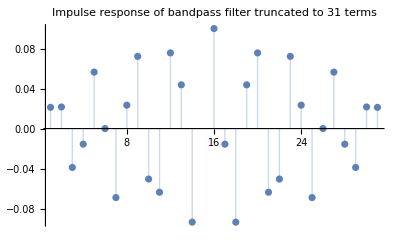

```mathematica
L=31;firBP=Table[bpKer[n],{n,-(L-1)/2,(L-1)/2}];
ListPlot[firBP, PlotRange->All,Filling->Axis,PlotLabel->"Impulse response of bandpass filter truncated to 31 terms"]
```

```mathematica
firBP
```

{0.0212207,0.0216236,-0.0388775,-0.0155915,0.0564582,0,-0.0690045,0.0233872,0.0722011,-0.0504551,-0.063662,0.0756827,0.0437373,-0.0935489,Piecewise[{{InverseFourierTransform[1,ω,-1,FourierParameters→{1,-1}], -1.88496≤ω<-1.5708||1.5708≤ω<1.88496}, {0, True}}],0.1,-0.0155792,-0.0935489,0.0437373,0.0756827,-0.063662,-0.0504551,0.0722011,0.0233872,-0.0690045,0,0.0564582,-0.0155915,-0.0388775,0.0216236,0.0212207}

It is always advisable in filter design to check and make sure that the design worked, in this case, that it really is a bandpass filter. This is accomplished by looking at the DFT of the (truncated) kernel

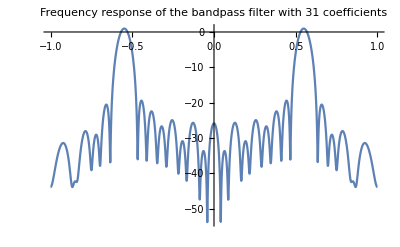

```mathematica
Plot[20 Log[10,Abs[freqZ[firBP,ω]]],{ω,-1,1},PlotLabel->"Frequency response of the bandpass filter with 31 coefficients"]
```

Check to see that it really is the same bandpass filter that we specified by plotting on the same axes as the specification:

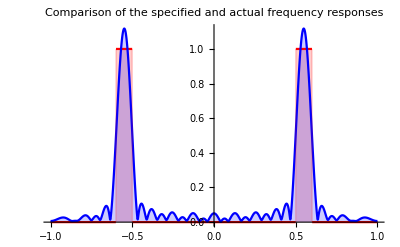

```mathematica
Plot[{bandPassSpec[ω],Abs[freqZ[firBP,ω]]},{ω,-1,1},PlotStyle->{Hue[0],Hue[2/3]},Filling->Axis, PlotRange->All,PlotLabel->"Comparison of the specified and actual frequency responses"]
```

### Numerical Design of a Band Pass Filter

Sometimes Mathematica can't carry out the Inverse Fourier Transform analytically. In this case, it is always possible to resort to a numerical approximation. To illustrate, consider the same desired bandpass shape.

```mathematica
bandPassSpec[ω_]:=UnitStep[ω+0.6]-UnitStep[ω+0.5]+UnitStep[ω-0.5]-UnitStep[ω-0.6];
Plot[bandPassSpec[ω],{ω,-1,1},PlotStyle->{Hue[0],Thick},Filling->Axis,PlotLabel->"Specification of bandpass filter"]
```

-Graphics-

This can be sampled several ways, but there are some possible pitfalls. When taking the transform of a real valued signal, the Fourier transform has certain symmetries (as in the above, the positive and the negative frequencies must be mirror images of each other. If the above waveform is sampled haphazardly, the samples will lack the symmetry (for instance, the positive bump on the right might contain one more or one less +1 value than the “same” hump on the left). If this happens, the inversion will be wrong, and the design will (with high likelihood) fail. Here’s a trial and error way. You can verify that the symmetry is correct this way for the imaginary part to be (essentially) zero. But change that -2 to anything else and you’re doomed.

```mathematica
sampBP = Drop[Table[bandPassSpec[n],{n,-1,1,(2/1000)}],-2];
```

A smarter way is to build the desired symmetry from the values at the positive frequencies:

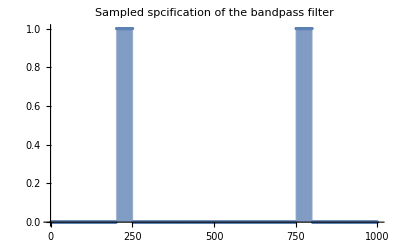

```mathematica
sampHalf = Table[bandPassSpec[n],{n,0,1,(1/500)}];
sampBP = Flatten[{Reverse[Drop[sampHalf,1]],Drop[sampHalf,-1]}];
ListPlot[sampBP, Filling->Axis,PlotLabel->"Sampled spcification of the bandpass filter"]
```

Next, the signal must be derotated it so that it is back in the form to use as input to the InverseFourier[ ] command

```mathematica
rotSampBP = RotateLeft[sampBP,Floor[Length[sampBP]/2]];
sampgBP = InverseFourier[rotSampBP, FourierParameters->{1,-1}];
```

If the symmetry is right, the Im[] part is near zero. Here is a check:

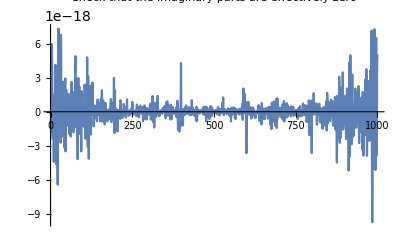

```mathematica
ListPlot[Im[sampgBP],Joined->True, PlotRange->All,PlotLabel->"Check that the imaginary parts are effectively zero"]
```

Since 10^(-18) is effectively round off error, the symmetry checks. Need to RotateLeft[] half the length in order to center the impulse response (otherwise half of it appears at the left and half at the right hand sides).

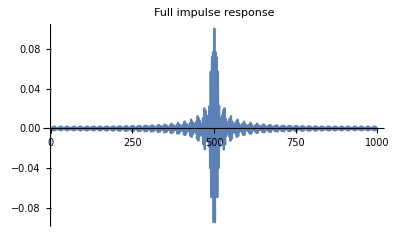

```mathematica
mid = Floor[Length[sampBP]/2];
rotSampgBP = RotateLeft[Re[sampgBP],mid];
ListPlot[rotSampgBP,Joined->True, PlotRange->All,PlotLabel->"Full impulse response"]
```

Zoom in to impulse response more closely. It looks (something like) a damped sinusoid...

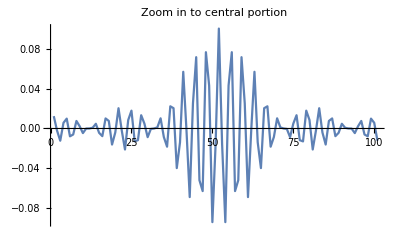

```mathematica
ListPlot[rotSampgBP[[mid-50;;mid+50]],Joined->True, PlotRange->All,PlotLabel->"Zoom in to central portion"]
```

Truncate to a normal length

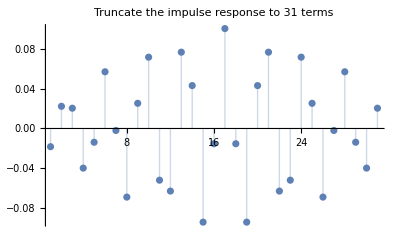

```mathematica
L=31; 
samphBP = rotSampgBP[[mid-Floor[L/2];;mid+Floor[L/2]]];
ListPlot[samphBP,PlotRange->All,Filling->Axis,PlotLabel->"Truncate the impulse response to 31 terms"]
```

Check to see that it really is a bandpass filter

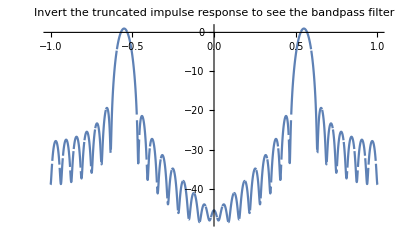

```mathematica
Plot[20 Log[10,Abs[freqZ[samphBP,ω]]],{ω,-1,1},PlotLabel->"Invert the truncated impulse response to see the bandpass filter"]
```

Check to see that it really is the right bandpass filter that we specified

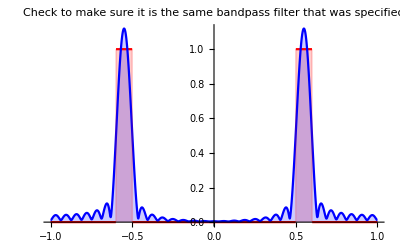

```mathematica
Plot[{bandPassSpec[ω],Abs[freqZ[samphBP,ω]]},{ω,-1,1},PlotStyle->{Hue[0],Hue[2/3]},Filling->Axis, PlotRange->All,PlotLabel->"Check to make sure it is the same bandpass filter that was specified"]
```

### FIR Filter Design

The intent of the above sections was to show the reasoning behind every step of the filter design procedure. This section presents a function that carries out the complete procedure from a direct specification in the frequency domain and a second function that checks the design to make sure it works. Most of the code in both designFIR[ ] and checkDesign[ ] should be familiar from the above discussion. The main difference is in detailed form of the specification, instead of creating a functional form for the spec, a straight line approximation is used.

```mathematica
designFIR[filterSpec_,L_]:=Module[{fSpec=filterSpec,fSpecCont,sampHalf,samp,rotSamp,sampg,mid,rotSampg},If[First[fSpec][[1]]≠0,fSpec=Prepend[fSpec,{0,0}];];
If[Last[fSpec][[1]]≠1,fSpec=Append[fSpec,{1,0}];];
If[Length[Select[Differences[Transpose[fSpec][[1]]],#<0&]]>0,Print["filterSpec is not in ascending order"];Abort[]];
fSpecCont=Interpolation[fSpec,InterpolationOrder->1];
sampHalf=Table[fSpecCont[n],{n,0,1,1/512}];
samp=Flatten[{Reverse[Drop[sampHalf,1]],Drop[sampHalf,-1]}];
rotSamp=RotateLeft[samp,Floor[Length[samp]/2]];
sampg=InverseFourier[rotSamp,FourierParameters->{1,-1}];
mid=Floor[Length[samp]/2];
rotSampg=RotateLeft[Re[sampg],mid];
samph=rotSampg[[mid-Floor[L/2];;mid+Floor[L/2]]]];
```

As an example, consider re-designing the same filter as above. The specification is that the filter should be zero between DC and 0..5, one between 0.5 and 0.6, and zero for frequencies between 0.6 and 1. This specification is encoded exactly like the inputs to ListPlot[ ]

```mathematica
filterSpec={{0,0},{0.499,0.0},{0.5,1.0},{0.599,1},{0.6,0},{1,0}};
```

allowing them to be easily checked.

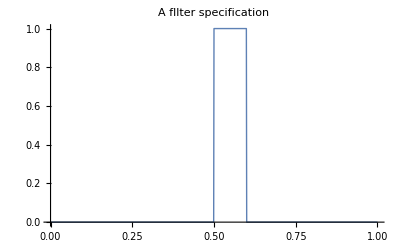

```mathematica
ListLinePlot[filterSpec,PlotStyle->Thick,PlotLabel->"A fllter specification"]
```

Then the design is:

```mathematica
desFilter=designFIR[filterSpec,31];
```

check the design of in designFIR to see agreement between spec and actual filter

```mathematica
checkDesign[filterSpec_,desFilter_,imageSize_,type_]:=Module[{fSpec=filterSpec,fSpecCont,check,func},If[First[fSpec][[1]]≠0,fSpec=Prepend[fSpec,{0,0}];];
If[Last[fSpec][[1]]≠1,fSpec=Append[fSpec,{1,0}];];
fSpecCont=Interpolation[fSpec,InterpolationOrder->1];
check[ω_]:=Sum[desFilter[[i]] Exp[-I Pi ω (i-1)],{i,1,Length[desFilter]}];
If[type=="Log",func=Log,func=Identity];
Plot[{func[fSpecCont[ω]],func[Abs[check[ω]]]},{ω,0,1},PlotStyle->{Hue[0],Hue[2/3]},PlotRange->All,ImageSize->imageSize]];
```

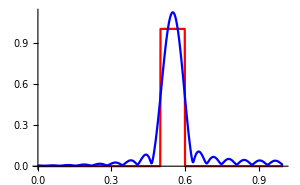
-Graphics-Checking that the design meets the specs

```mathematica
Labeled[checkDesign[filterSpec,desFilter,300,"Linear"],"Checking that the design meets the specs",LabelStyle->captionStyle]
```

The design is almost the same as above: it differs only because the transition from 0 to 1 is done over the range 0.499 to 0.5 instead of instantaneously as in the original design. Using designFIR[ ] it is easy to create any desired filter. Here’s an example.

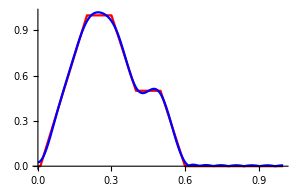
-Graphics-Another filter design example: red=spec, blue=designed filter

```mathematica
filterSpec2={{0,0},{0.01,0.0},{0.2,1.0},{0.3,1},{0.4,1/2},{0.5,1/2},{0.6,0},{1,0}};
desFilter2=designFIR[filterSpec2,31];
Labeled[checkDesign[filterSpec2,desFilter2,300,"Linear"],"Another filter design example: red=spec, blue=designed filter",LabelStyle->captionStyle]
```

How many filter coefficients are needed to get a good design?  With the filter above:

```mathematica
labelFilterOrder="Increase filter order to get closer to specification";
infoFilterOrder="The desired frequency response is plotted in red.\n\nChoose a filter order (with the slider).\n\nThe demonstration designs a filter with the specified order (using designFIR[]) and plots the frequency response of the resulting design in blue.\n\nIncrease the filter order to make the design closer to the specification.\n\nDecrease the filter order and the designed filter becomes less like the desired frequency response.";
Manipulate[
desFilter2=designFIR[filterSpec2,filtOrd];
checkDesign[filterSpec2,desFilter2,300,"Linear"],
Row[{Control[{{filtOrd,10,"filter order"},2,50,1,Appearance->"Labeled"}],Spacer[20],info[infoFilterOrder]}],FrameLabel->Style[labelFilterOrder,Medium],TrackedSymbols->{filtOrd},SaveDefinitions->True]
```

Order 10 isn’t high enough to get an accurate design. By the time the order increases to about 25 or 30, this matches reasonably well.

HW: Design a high pass filter that attenuates all frequencies below 0.2 and passes all frequencies above. What order did you choose and why?

HW: Design a “notch” filter that passes all frequencies except those in a band between 0.1 and 0.2. What order do you choose?

HW: Design a bandpass filter than passes only frequencies between f and 1.01f. Explain what you see. Does it matter what f you choose? Does it matter what order you choose?

```mathematica
labelFilterSpec3="A bandpass filter that passes frequencies between f and 1.01f";
infoFilterSpec3="Choose the center frequency to change the (narrow) band of frequencies the filter will pass; the desired frequency response is plotted in red.\n\nChoose a filter order (with the slider).\n\nThe demonstration designs a filter with the specified order (using designFIR[]) and plots the frequency response of the resulting design in blue.\n\nIncrease the filter order to make the design closer to the specification.\n\nDecrease the filter order and the designed filter becomes less like the desired frequency response.";
filterSpec3[f_]:={{0,0},{f-0.005,0.0},{f,1},{f+0.01,1},{f+0.015,0},{1,0}};
Manipulate[desFilter3=designFIR[filterSpec3[f3],filtOrd3];
checkDesign[filterSpec3[f3],desFilter3,300,"Linear"],
Row[{Control[{{filtOrd3,10,"filter order"},2,300,1,Appearance->"Labeled"}],Spacer[20],info[infoFilterSpec3]}],{{f3,0.3,"center frequency"},0.01,0.9,Appearance->"Labeled"},
FrameLabel->Style[labelFilterSpec3,Medium],TrackedSymbols->{filtOrd3,f3},SaveDefinitions->True]
```

### Two-Dimensional Filter Design

In two dimensions, as in one, it is possible to specify filters in the frequency domain and to transform back into the spatial domain to find the kernel. This section designs a 2D bandpass filter.

```mathematica
bandPass2D[x_,y_,c1_, c2_]:=Exp[-c1 (y^2+x^2)]-Exp[-c2 (y^2+x^2)];
Plot3D[bandPass2D[x,y,14.8,22.7],{x,-1,1},{y,-1,1}, Filling->Axis, PlotRange->All,PlotLabel->"A 2D bandpass filter specification"]
```

-Graphics3D-

The impulse response of this BP frequency response is given by the IFT

```mathematica
InverseFourierTransform[bandPass2D[x/Pi,y/Pi,14.8,22.7],{x,y },{j,k },FourierParameters->{1,-1}]
```

0.0530674 ⅇ^(-0.166716 j^2-0.166716 k^2)-0.034599 ⅇ^(-0.108696 j^2-0.108696 k^2)

```mathematica
bandPassKer2D[j_,k_]:=0.0530674 E^(-0.166716 j^2-0.166716 k^2)-0.034599 E^(-0.108696 j^2-0.108696 k^2)
```

Truncate to a few terms

```mathematica
L=11;
bpKernel2D = N[Table[bandPassKer2D[j,k],{j,-Floor[L/2],Floor[L/2]},{k,-Floor[L/2],Floor[L/2]}]];
ListPlot3D[bpKernel2D,PlotRange->All,PlotLabel->"The impulse response truncated to 11 by 11"]
```

-Graphics3D-

Check to make sure it's correct:

```mathematica
Plot3D[Abs[freqZ2[bpKernel2D,w,v]],{w,-1,1},{v,-1,1},PlotRange->All,PlotLabel->"The frequency response of this filter"]
```

-Graphics3D-

How close is this truncated design to the specification?

```mathematica
Plot3D[Abs[freqZ2[bpKernel2D,w,v]]-Abs[bandPass2D[w,v,14.8,22.7]],{w,-1,1},{v,-1,1},PlotRange->All,PlotLabel->"This is the error between the spec and the design"]
```

-Graphics3D-

Not very close, but good enough to show what's happening. So far, this is exactly like the analytical design where the specified frequency response could be inverted (using InverseFourierTransform[ ]) back into the impulse response. But suppose that this calculation had failed, that is, we couldn't find the analytic form of bandPassKer2D[ ]. Then we could do it numerically. Begin by sampling bandPass2D[ ] at the desired L=11 points.

```mathematica
sampledhBP = Table[bandPass2D[x,y,14.8,22.7],{x,-1,1,2/L},{y,-1,1,2/L}];
```

How good is the sampling?

```mathematica
ListPlot3D[sampledhBP, PlotRange->All,PlotLabel->"Sampling the bandpass design"]
```

-Graphics3D-

That's terrible. There is hardly any dip in the middle -- this BP looks more like a LP. Better try again with more samples.

```mathematica
sampledhBP2 = Table[bandPass2D[x,y,14.8,22.7],{x,-1,1,2/500},{y,0,1,1/250}];
ListPlot3D[sampledhBP2, PlotRange->All,PlotLabel->"Sampling with more points yields better results"]
```

-Graphics3D-

Much better! This needs to be made symmetric in order to have a real-valued inverse FT.

```mathematica
sam = sampledhBP2;
{hor,ver}=Dimensions[sam];
n = Max[Floor[ver/2],Floor[hor/2]];
outmat = ConstantArray[0,{2 n, 2 n}];
sam[[n+2;;2 n,1]] = Reverse[sam[[2;;n,1]]];
outmat[[All,n+1;;2 n]]=sam[[1;;2 n,1;;n]];
outmat[[2;;2 n, 2;;n]]=Reverse[sam[[2;;2 n,2;;n]],{1,2}];
outmat[[All,1]]=Flatten[{0,Reverse[sam[[n+2;;2 n,n+1]]],sam[[n+1;;2 n,n+1]]}];
outmat[[1,2;;n]] = Reverse[sam[[1,2;;n]]]; 
symBP = outmat;
```

This can now be inverted numerically:

```mathematica
impBP = InverseFourier[RotateLeft[symBP,{251,251}],FourierParameters->{1,-1}];
{lenH,lenV}=Dimensions[impBP]; centeredImpBP = RotateLeft[impBP,{Floor[lenH/2],Floor[lenV/2]}];
L=31;mid=Floor[lenH/2];
kerBP=Table[Re[centeredImpBP[[n,m]]],{n,mid-Floor[L/2],mid+Floor[L/2]},{m,mid-Floor[L/2],mid+Floor[L/2]}];
ListPlot3D[kerBP,PlotRange->All,PlotLabel->"The desired impulse response"]
```

-Graphics3D-

```mathematica
Plot3D[Abs[freqZ2[kerBP,w,v]],{w,-1,1},{v,-1,1},PlotRange->All,PlotLabel->"Check that the impulse response is close to the specification"]
```

-Graphics3D-